```mathematica
ClearAll["Global'*"];
$PrePrint = MatrixForm;
```

```mathematica
(*Definicje stałych i funkcji*)
G=.01;
H=1;
rho0=1;
ymax=10;
v0[y_]:=(H y (*+ 0.1 Sin[20Pi y / (2 ymax)] *))
rho0y[y_]:=(
rho0 + 0.1 Sin[20Pi y / (2 ymax)](**)
)
m[y_]:=(Integrate[rho0y[yy],{yy,0,y}])

xi[y_,t_]:=(y+v0[y]t-2Pi G m[y]t^2)
a[t_]:=1+H t- 2 Pi G rho0 t^2   (*czynnik skali dla rho0y = const*)
xiDy[y_,t_]:=(1+(H (*+Pi/10 Cos[20 Pi y / (2ymax)]*))t-2Pi G rho0y[y] t^2) (*pochodna xi po y*)
xiDt[y_,t_]:=(v0[y]-4Pi G m[y]t) (*pochodna xi po t*)
tCollapse[y_]:=(t/.Solve[xi[y,t]==0,t][[2]])
tMerge[y_]:=(
(H + Sqrt[H^2+4 Pi G rho0y[y]])/(4 Pi G rho0y[y])
)

rhokt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k xi[y,t]],{y,-ymax,ymax}]
)

vkt[k_,t_]:=(
NIntegrate[xiDt[y,t]Exp[-I k xi[y,t]]xiDy[y,t],{y,-ymax,ymax}]
)

rhokScaledt[k_,t_]:=(
NIntegrate[rho0y[y] Exp[-I k / a[t]   xi[y,t]],{y,-ymax,ymax}]
)

vkScaledt[k_,t_]:=(
NIntegrate[xiDt[y,t]Exp[-I k /a[t] xi[y,t]]xiDy[y,t],{y,-ymax,ymax}]
)

rhotxScaled[x_,t_]:=(
rho0y[(x/a[t])/a[t]]Abs[xiDy[(x/a[t])/a[t] ,t]]^(-1)
)

momentumDensityScaled[x_,t_]:=(
rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1) xiDt[(x/a[t]),t]
)
```

```mathematica
tmax=Re[NMaximize[tCollapse[y],y][[1]]];
tbounce=Max[t/.{Solve[xiDt[-ymax,t]==0,t][[1]],Solve[xiDt[ymax,t]==0,t][[1]]}];
ta0=t/.Solve[{a[t]==0, 0≤t≤tmax},t][[1]];
amax=FindMaximum[a[t],{t,tmax/2}][[1]];
Print["tmax: ",tmax, ", tbounce ",tbounce,", t[a=0] ",ta0,", amax ",amax]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

tmax: 18.1065, tbounce 7.95775, t[a=0] 16.8595, amax 4.97887

```mathematica
tstep=.05;
ts=Table[t,{t,0,tmax,tstep}];
k=10;
rhokScaled1=rhokScaledt[k,ts];
vkScaled1=vkScaledt[k,ts];
(*rhok1=rhokt[k,ts];
vk1=vkt[k,ts];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-7.96875}. NIntegrate obtained 0.0125914-0.0160567 ⅈ and 2.37077×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-9.96094}. NIntegrate obtained 0.0000190707-0.0204577 ⅈ and 5.50977×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(*Wykresy 10 modu przeskalowanej transformaty gęstości*)
ListLinePlot[Thread[{ts,Re[rhokScaled1]}],PlotLabels->{"Re"}, PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Im[rhokScaled1]}],PlotLabels->{"Im"},PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Abs[rhokScaled1]^2}],PlotLabels->{"| |^2"},PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{\\rho}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Wykresy 10 modu przeskalowanej transformaty prędkości*)
ListLinePlot[Thread[{ts,Re[vkScaled1]}],PlotLabels->{"Re"}, PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{v}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Im[vkScaled1]}],PlotLabels->{"Im"},PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{v}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
ListLinePlot[Thread[{ts,Abs[vkScaled1]^2}],PlotLabels->{"| |^2"},PlotLabel->"k=10",AxesLabel->{"t",ToExpression["\\hat{v}",TeXForm]},GridLines->{{{tbounce,Red},{ta0,Red}},None},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Wyresy pierwszego modu transformat gęstości i prędkości*)
(*tymczasowo nieliczone - trzeba odkomentować rhok1 i vk1*)
ListLinePlot[Thread[{ts,Re[rhok1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Im[rhok1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Abs[rhok1]^2}],PlotLabels->{"Modul kwadrat"},PlotLabel->"k=1",AxesLabel->{"t",ToExpression["\\rho",TeXForm]},GridLines->{{{tbounce,Red}},None}]
ListLinePlot[Thread[{ts,Re[vk1]}],PlotLabels->{"Re"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
ListLinePlot[Thread[{ts,Im[vk1]}],PlotLabels->{"Im"},PlotLabel->"k=1",AxesLabel->{"t","v"}]
```

```mathematica
(*Wykres xi*)
Plot3D[xi[y,t],{y,-ymax,ymax},{t,0,tmax},PlotRange->All,AxesLabel->Automatic]
```

-Graphics3D-

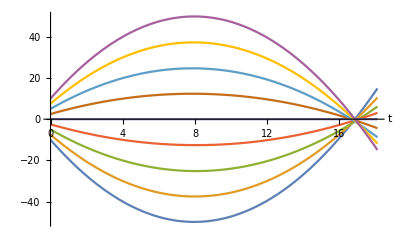

```mathematica
(*Trajektorie*)
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,0,tmax},AxesLabel->Automatic]
```

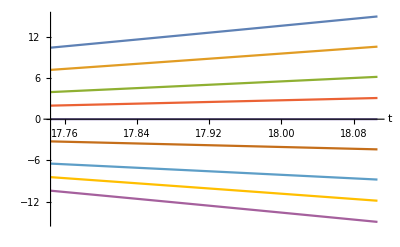

```mathematica
Plot[Evaluate@Table[xi[y,t],{y,-ymax,ymax,2.5}],{t,tmax*.98,tmax},AxesLabel->Automatic]
```

```mathematica
(*wykres przeskalowanej gęstości: rho[x/a[t],t] dla rho[y]=rho0 *)
rhotxScaled[x_,t_]:=(rho0y[(x/a[t])]Abs[xiDy[(x/a[t]) ,t]]^(-1))
Plot3D[rhotxScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Wykres przeskalowanej gęstości pędu [x/a[t]]*)
Plot3D[momentumDensityScaled[x,t],{x,-ymax*amax,ymax*amax},{t,0,tmax},AxesLabel->{"x","t"}]
```

-Graphics3D-

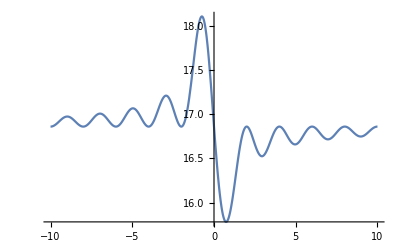

```mathematica
Plot[tCollapse[y],{y,-ymax,ymax},PlotRange->All]
```

```mathematica
(*Rozwiązanie równań pierwszego zaburzenia*)
sol=NDSolve[{dv'[t]== I 4 Pi G drho[t] /(k a[t])^2,drho'[t]==-I k rho0/a[t]^3,drho[0]==-.1,dv[0]==0},{dv[t],drho[t]},{t,0,ta0} ]
```

NDSolve::ndsz: At t == 16.8595, step size is effectively zero; singularity or stiff system suspected.

(dv[t]→InterpolatingFunction[…][t] | drho[t]→InterpolatingFunction[…][t])

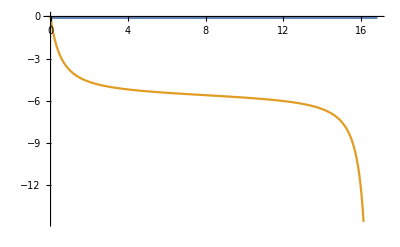

```mathematica
Plot[Evaluate[{Re[drho[t]],Im[drho[t]]}/.sol],{t,0,ta0}]
```

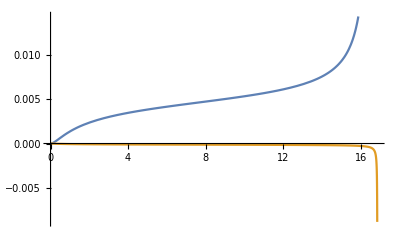

```mathematica
Plot[Evaluate[{Re[dv[t]],Im[dv[t]]}/.sol],{t,0,ta0}]
```